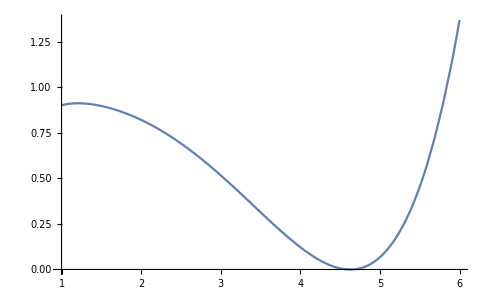

```mathematica
Clear[k,m,ss,om,jj];
(*m1r=k r^3;
m2r=m;
msr= 4 Pi ss r^2;*)
k=0.01;
m=1;
om=0.2;  (* ω *)
jj=0.1;
Omega=2 jj/x^3;  (* Ω *)
ss=0.001/x^2;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2=m^4 x^3(-16 π^2 ss^2 x+(16 π^2 ss^2 x^5 m^3 om^2)/(x-2)+(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2);
q4=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f1=Plot[q0,{x,1, 6},PlotRange->All]
```

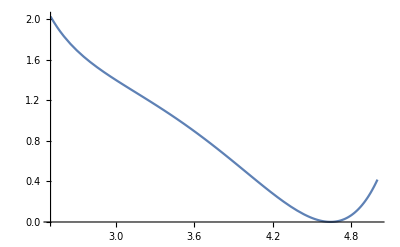

```mathematica
f1a=Plot[q2,{x,2.5, 5},PlotRange->All]
```

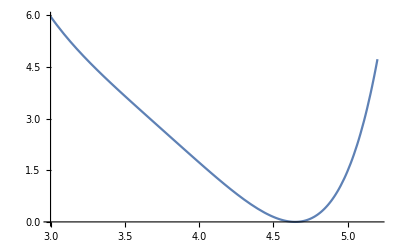

```mathematica
f1b=Plot[q4,{x,3, 5.2},PlotRange->All]
```

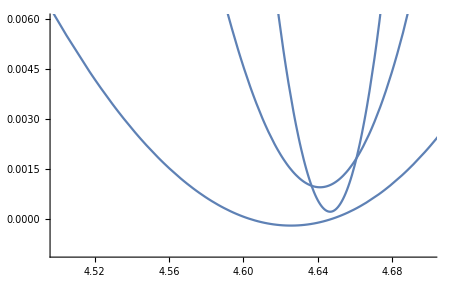

```mathematica
Show[f1,f1a,f1b,PlotRange->{{4.5,4.7},{-0.001,0.006}}]
```

```mathematica
q01=FullSimplify[q0]
```

(4.73741×10^-6+x (-0.06+x (6.23418×10^-9+x (0.000159493+0.980442 x+1.57914×10^-6 x^3-0.0198 x^4+0.0001 x^7))))/x^4

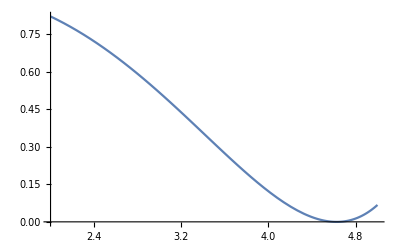

```mathematica
Plot[q01,{x,2,5}]
```

```mathematica
q01p=D[q01,x]
```

1/x^4(-0.06+x (6.23418×10^-9+x (0.000159493+0.980442 x+1.57914×10^-6 x^3-0.0198 x^4+0.0001 x^7))+x (6.23418×10^-9+x (0.000159493+0.980442 x+1.57914×10^-6 x^3-0.0198 x^4+0.0001 x^7)+x (0.000159493+0.980442 x+1.57914×10^-6 x^3-0.0198 x^4+0.0001 x^7+x (0.980442+4.73741×10^-6 x^2-0.0792 x^3+0.0007 x^6))))-(4 (4.73741×10^-6+x (-0.06+x (6.23418×10^-9+x (0.000159493+0.980442 x+1.57914×10^-6 x^3-0.0198 x^4+0.0001 x^7)))))/x^5

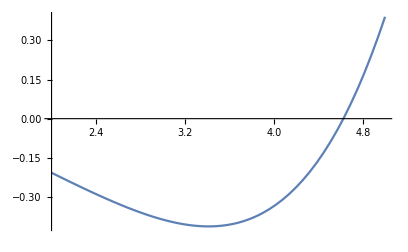

```mathematica
Plot[q01p,{x,2,5},PlotRange->All]
```

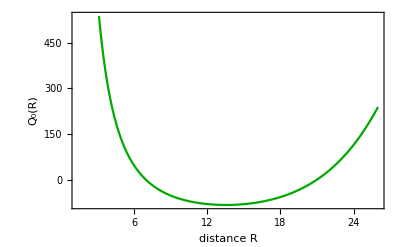

```mathematica
Clear[k,m,ss,om,jj];(*m1r=k r^3; m2r=m; msr= 4 Pi ss r^2;*)
k=0.001;
m=1;
om=0.2;  (* ω *)
jj=0.1;
Omega=2 jj/x^3;  (* Ω *)
ss=1/x^2;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0a=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2a=m^4 x^3(-16 π^2 ss^2 x+(16 π^2 ss^2 x^5 m^3 om^2)/(x-2)+(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2);
q4a=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f2=Plot[q0a,{x,1.4,26},Frame->True,FrameLabel->{"distance R"," Q_0(R)"},PlotStyle->{Darker[Green]},AxesStyle->Black,Axes->{True,False},  LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

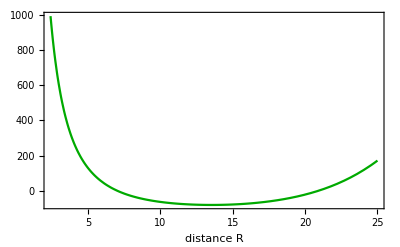

```mathematica
f20=Plot[q0a,{x,2.4,25},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Green]},Axes->{True,False},PlotRange->All, AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

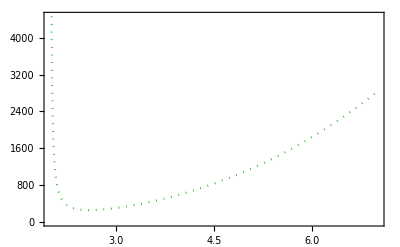

```mathematica
f2a=Plot[q2a,{x,2,7},Frame->True,PlotStyle->{Dotted,Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

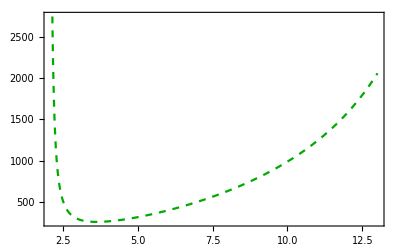

```mathematica
f2b=Plot[q4a,{x,2.1,13},Frame->True,PlotStyle->{Dashed,Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

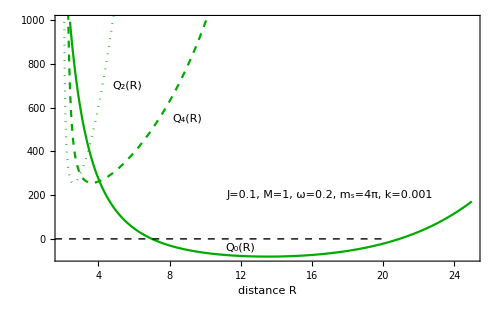

```mathematica
fig2am=Show[f20,f2a,f2b, Graphics[{Inset[Framed["J=0.1, M=1, ω=0.2, m_s=4π, k=0.001"],{17,200},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{5.6,700},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{12,-40},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)",{9,550},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-80,1000}]
```

```mathematica
Export["D:ffig2am.pdf",fig2am,"PDF"];
Export["D:ffig2am.eps", fig2am];
```

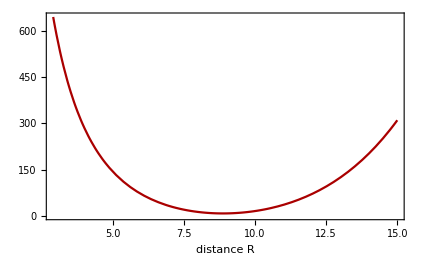

```mathematica
Clear[k,m,ss,om,jj];(*m1r=k r^3; m2r=m; mmsr= 4 Pi ss r^2;*)
k=0.005;
m=1;
om=0;  (* ω *)
jj=0;
Omega=2 jj/x^3;  (* Ω *)
ss=1/x^2;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0b=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2b=m^4 x^3(-16 π^2 ss^2 x+(16 π^2 ss^2 x^5 m^3 om^2)/(x-2)+(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2);
q4b=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f3=Plot[q0b,{x,2.9,15},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Red]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->{True,False}]
```

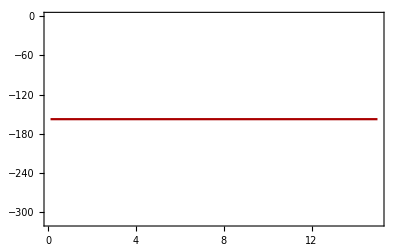

```mathematica
f3a=Plot[q2b,{x,0.1,15},Frame->True,PlotStyle->{Darker[Red]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->{True,False}]
```

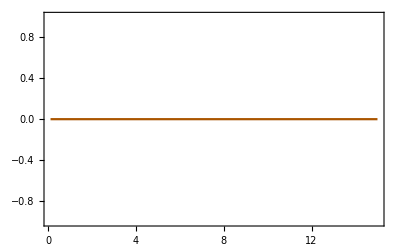

```mathematica
f3b=Plot[q4b,{x,0.1,15},Frame->True,PlotStyle->{Darker[Orange]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

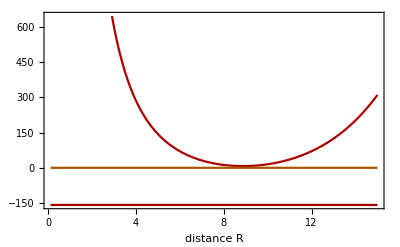

```mathematica
Show[f3,f3a,f3b,PlotRange->All]
```

```mathematica
(*****************************************************************************************************************************************)
```

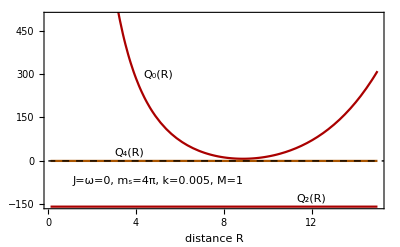

```mathematica
fd02ms=Show[f3,f3a,f3b,Graphics[{Inset[Framed["J=ω=0, m_s=4π, k=0.005, M=1"],{5,-70},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)",{3.7,30},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{12,-130},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{5,300},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},ImageSize->400,PlotRange->{-152,500},Axes->False]
```

```mathematica
Export["D:fd02ms.pdf",fd02ms,"PDF"];
Export["D:fd02ms.eps", fd02ms];
```